```mathematica
(* set the directory we want *) 
SetDirectory[NotebookDirectory[]];
files=FileNames["*.txt",NotebookDirectory[]]
data=Import[#,"Data"]&/@files;
```

{/Users/tomi/liquid_sensing/mathematica_anlysis /orangejuice.txt,/Users/tomi/liquid_sensing/mathematica_anlysis /output.txt,/Users/tomi/liquid_sensing/mathematica_anlysis /saltwater.txt,/Users/tomi/liquid_sensing/mathematica_anlysis /tapwater.txt}

```mathematica
orange = Drop[data[[1]],1];
saltwater = Drop[data[[2]],1];
tapwater = Drop[data[[3]],1];



(* correct to zero time *) 
orange[[;;,{1}]]=orange[[;;,{1}]]-orange[[1,1]];

(* convert to MO *) 
orange[[;;,{2}]]=orange[[;;,{2}]]/10^6;
orange[[;;,{3}]]=orange[[;;,{3}]]/10^6;
orange[[;;,{4}]]=orange[[;;,{4}]]/10^6;



(* correct to zero time *) 
saltwater[[;;,{1}]]=saltwater[[;;,{1}]]-saltwater[[1,1]];

(* convert to MO *) 
saltwater[[;;,{2}]]=saltwater[[;;,{2}]]/10^6;
saltwater[[;;,{3}]]=saltwater[[;;,{3}]]/10^6;
saltwater[[;;,{4}]]=saltwater[[;;,{4}]]/10^6;

(* correct to zero time *) 
tapwater[[;;,{1}]]=tapwater[[;;,{1}]]-tapwater[[1,1]];

(* convert to MO *) 
tapwater[[;;,{2}]]=tapwater[[;;,{2}]]/10^6;
tapwater[[;;,{3}]]=tapwater[[;;,{3}]]/10^6;
tapwater[[;;,{4}]]=tapwater[[;;,{4}]]/10^6;
```

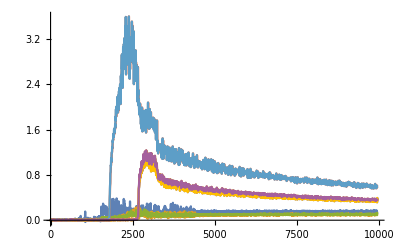

```mathematica
ListPlot[{orange[[;;,{1,2}]],orange[[;;,{1,3}]],orange[[;;,{1,4}]],saltwater[[;;,{1,2}]],saltwater[[;;,{1,3}]],saltwater[[;;,{1,4}]],tapwater[[;;,{1,2}]],tapwater[[;;,{1,3}]],tapwater[[;;,{1,4}]]},Joined->True,PlotRange->All,InterpolationOrder->30]
```

```mathematica
avorange = MovingAverage[orange,10];
avsaltwater = MovingAverage[saltwater,10];
avsaltwater = MovingAverage[saltwater,10]
```

```mathematica
smoothplot = ListPlot[{avdata[[;;,{1,2}]],avdata[[;;,{1,3}]],avdata[[;;,{1,4}]]},Joined->True,PlotRange->All,InterpolationOrder->4,Frame->True, FrameLabel->{{"Restivity [M Ohms]",""},{" Time [mS]","Conductivity Decay"}},ImageSize->Full];

(* top 60% (from max value - use as average) *) 
top60 = Max[avdata[[;;,{2}]]]/100*60;
topdata = Cases[avdata[[;;,{1,2}]],{_,y_}/;y>top60];
topdataav = topdata[[;;,2]];
Mean[topdataav];
```

smoothplot.png